```mathematica
(* Import the FEM package *)
Needs["NDSolve`FEM`"]
(* Define a set of geometric shapes which will constitute the domain *)
Subscript[T, 1]=Triangle[{{-1,1},{-1,3},{-3,1}}];
Subscript[T, 2]=Triangle[{{-3,1},{-1,-1},{-1,1}}];
Subscript[T, 3]=Triangle[{{1,-1},{1,-3},{3,-1}}];
Subscript[R, 1]=Rectangle[{-1,-1},{1,1}];
Subscript[R, 2]=Rectangle[{1,-1},{3,1}];
```

```mathematica
(* Combine the shapes to the domain *)
ID1 = RegionUnion[Subscript[T, 1],Subscript[T, 2],Subscript[T, 3],Subscript[R, 1],Subscript[R, 2]]
```

RegionUnion[Rectangle[{-1,-1},{1,1}],Rectangle[{1,-1},{3,1}],Triangle[{{-3,1},{-1,-1},{-1,1}}],Triangle[{{-1,1},{-1,3},{-3,1}}],Triangle[{{1,-1},{1,-3},{3,-1}}]]

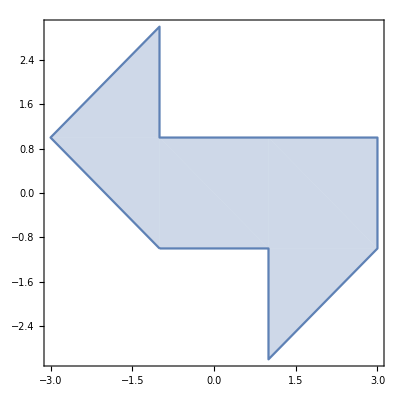

```mathematica
RegionPlot[ID1]
```

```mathematica
(* Create a mesh for the domain *)
(*meshID1=ToElementMesh[ID1,"MeshOrder"->2,MaxCellMeasure->0.01,"MaxBoundaryCellMeasure"->0.005,"BoundaryMeshGenerator"->"RegionPlot","NodeReordering"->True];*)
```

```mathematica
(*meshID1["Wireframe"]*)
```

```mathematica
(* define the vector field for the linear part *)
v[x_,y_]:={y,-x};
(*define the constants *)
ω=100000;
c=299792458;
α=-2*I*ω/c;
```

```mathematica
(* Discretize the PDE *)
(* 1 Variable data *)
Clear[VarData]
VarData = NDSolve`VariableData[{"DependentVariables"->{u},"Space"->{x,y}}]
```

{None,{x,y},{u},{},{},{},{},{}}

```mathematica
(* 2. Region *)
NumRegio = ToNumericalRegion[ID1]
```

NumericalRegion[RegionUnion[Rectangle[{-1,-1},{1,1}],Rectangle[{1,-1},{3,1}],Triangle[{{-3,1},{-1,-1},{-1,1}}],Triangle[{{-1,1},{-1,3},{-3,1}}],Triangle[{{1,-1},{1,-3},{3,-1}}]],{{-3,3},{-3,3}}]

```mathematica
(* 3. Create solution data *)
Clear[SolData]
SolData = NDSolve`SolutionData[{"Space"}->{NumRegio}]
```

{None,NumericalRegion[RegionUnion[Rectangle[{-1,-1},{1,1}],Rectangle[{1,-1},{3,1}],Triangle[{{-3,1},{-1,-1},{-1,1}}],Triangle[{{-1,1},{-1,3},{-3,1}}],Triangle[{{1,-1},{1,-3},{3,-1}}]],{{-3,3},{-3,3}}],{},{},{},{},{},{}}

```mathematica
(* 4. Initialize coefficients *)
Clear[Coeffs,Coefficients]
Coefficients = {"DiffusionCoefficients"->{{-IdentityMatrix[2]}}, "ReactionCoefficients"->{{1}}, "ConservativeConvectionCoefficients"->{{v[x,y]}}}
Coeffs = InitializePDECoefficients[VarData,SolData, Coefficients]
```

{DiffusionCoefficients→{{{{-1,0},{0,-1}}}},ReactionCoefficients→{{1}},ConservativeConvectionCoefficients→{{{y,-x}}}}

PDECoefficientData[<1,2>]

```mathematica
(* 5. Initialze boundary conditions *)
Subscript[Γ, D]=DirichletCondition[u[x,y]==0, True] (* simple Dirichlet BC everywhere *)
BCs = InitializeBoundaryConditions[VarData, SolData, {{Subscript[Γ, D]}}]
```

DirichletCondition[u[x,y]==0,True]

BoundaryConditionData[<1,2>]

```mathematica
(* 6. Set up method data *)
Clear[MethodData]
MethodData = InitializePDEMethodData[VarData,SolData, Method->{"FiniteElement","MeshOptions"->{ "MeshOrder"->2, "MaxCellMeasure"->0.01(*,"MaxBoundaryCellMeasure"->0.008*), "NodeReordering"->True}}]
```

FEMMethodData[<4793,{2},4>]

```mathematica
(* 7. Discretize the PDE *)
Clear[DiscretePDE]
DiscretePDE = DiscretizePDE[Coeffs,MethodData, SolData]
```

DiscretizedPDEData[<4793>]

```mathematica
(* Discretize the boundary conditions *)
(* 8. Discretizeboundary conditions *)
DiscreteBC = DiscretizeBoundaryConditions[BCs,MethodData, SolData]
```

DiscretizedBoundaryConditionData[<4793>]

```mathematica
{load,stiffness,damping,mass}=DiscretePDE["SystemMatrices"]
```

{SparseArray[<0>, {4793, 1}],SparseArray[<53609>, {4793, 4793}],SparseArray[<0>, {4793, 4793}],SparseArray[<0>, {4793, 4793}]}

```mathematica
MatrixPlot[damping]
```

-Graphics-

```mathematica
(* 9. Merge boundary conditions into matrices *)
DeployBoundaryConditions[{load,stiffness,damping,mass},DiscreteBC]
```

```mathematica
{load,stiffness,damping,mass}
```

{SparseArray[<0>, {4793, 1}],SparseArray[<50427>, {4793, 4793}],SparseArray[<400>, {4793, 4793}],SparseArray[<400>, {4793, 4793}]}

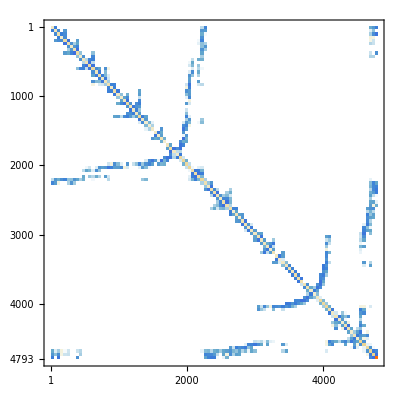

```mathematica
MatrixPlot[stiffness]
```

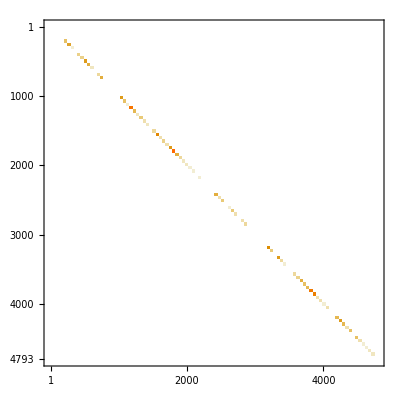

```mathematica
MatrixPlot[damping]
```

```mathematica
MatrixPlot[mass]
```

-Graphics-

```mathematica
Coeffs["Properties"]
```

{All,ConservativeConvectionCoefficients,Constraints,ConvectionCoefficients,DampingCoefficients,DiffusionCoefficients,Discrete,IndexedDiscrete,LoadCoefficients,LoadDerivativeCoefficients,MassCoefficients,Nonlinear,Parametric,Properties,ReactionCoefficients,SpatialDimension,Stationary,SystemSize,Transient}

```mathematica
Coeffs["DampingCoefficients"]
```

{{0}}

```mathematica
Coeffs["ReactionCoefficients"]
```

{{1}}

```mathematica
Transpose[damping]==damping
```

True

```mathematica
Transpose[mass]==mass
```

True

```mathematica
mass
```

SparseArray[<400>, {4793, 4793}]

```mathematica
A={{0,mass},{mass,0}}
```

{{0,SparseArray[<400>, {4793, 4793}]},{SparseArray[<400>, {4793, 4793}],0}}

```mathematica
B=SparseArray[{mass,-stiffness}]
```

SparseArray[<50827>, {2, 4793, 4793}]

```mathematica
Eigenvalues[{A,B},-10]
```

Eigenvalues::matsq: Argument {{{0,SparseArray[«1»]},{SparseArray[Automatic,«3»],0}},«1»} at position 1 is not a non-empty square matrix.

Eigenvalues[{{{0,SparseArray[<400>, {4793, 4793}]},{SparseArray[<400>, {4793, 4793}],0}},SparseArray[<50827>, {2, 4793, 4793}]},-10]

```mathematica
mass["Properties"]
```

{AdjacencyLists,Background,ColumnIndices,Density,NonzeroPositions,NonzeroValues,PatternArray,Properties,RowPointers}

```mathematica
Amat=SparseArray[ArrayFlatten[{{0,mass},{mass,damping}}]]
```

SparseArray[<1200>, {9586, 9586}]

```mathematica
Dimensions[Amat]
```

{9586,9586}

```mathematica
4793*2
```

9586

```mathematica
B
```

SparseArray[<50827>, {2, 4793, 4793}]

```mathematica
Dimensions[Amat]
```

{9586,9586}

```mathematica
Dimensions[B]
```

{2,4793,4793}

```mathematica
Clear[B]
B=SparseArray[ArrayFlatten[{{mass,0},{0,-stiffness}}]]
```

SparseArray[<50827>, {9586, 9586}]

```mathematica
Clear[A]
```

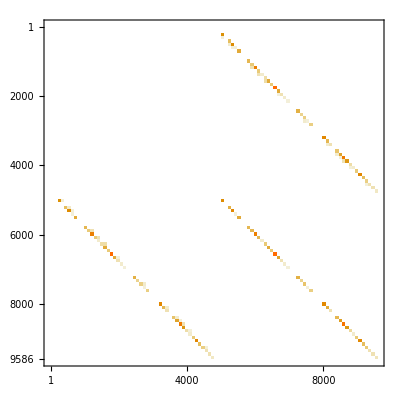

```mathematica
MatrixPlot[Amat]
```

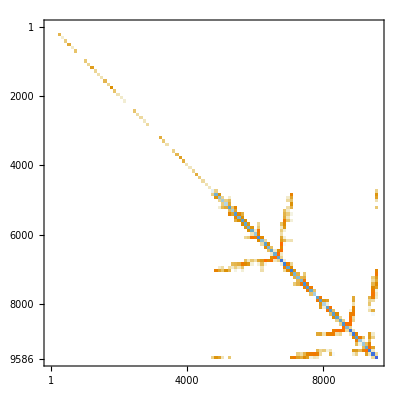

```mathematica
MatrixPlot[B]
```

```mathematica
Transpose[Amat]==Amat
```

True

```mathematica
Transpose[B]==B
```

False

```mathematica
Transpose[stiffness]==stiffness
```

False

```mathematica
(* the damping matrix must have a prefactor *)
```

```mathematica
Amat=SparseArray[ArrayFlatten[{{α*damping,stiffness},{stiffness,0}}]]
B=SparseArray[ArrayFlatten[{{-mass,0},{0,stiffness}}]]
```

SparseArray[<101254>, {9586, 9586}]

SparseArray[<50827>, {9586, 9586}]

```mathematica
B==Transpose[B]
```

False

```mathematica
Amat==ConjugateTranspose[Amat]
```

False

```mathematica
meshID1=ToElementMesh[ID1,"MeshOrder"->1,MaxCellMeasure->0.01,"BoundaryMeshGenerator"->"RegionPlot","NodeReordering"->True]
```

ElementMesh[{{-3.,3.},{-3.,2.92857}},{TriangleElement[<2296>]}]

```mathematica
(*Eigenvalues[{Amat,B},-10]*)
```

```mathematica
(* Eigenvalues obtained using NDEigenvalues *)
```

```mathematica
{L,Bcond}={Laplacian[u[t,x,y],{x,y}]+α*v[x,y].Grad[D[u[t,x,y],t],{x,y}]+D[u[t,x,y],{t,2}]==0,DirichletCondition[u[t,x,y]==0,True]}
```

{u^(0,0,2)[t,x,y]+u^(0,2,0)[t,x,y]-(100000 ⅈ (-x u^(1,0,1)[t,x,y]+y u^(1,1,0)[t,x,y]))/149896229+u^(2,0,0)[t,x,y]==0,DirichletCondition[u[t,x,y]==0,True]}

```mathematica
SetPrecision[NDEigenvalues[{L,Bcond},u[t,x,y],t,{x,y}∈NumRegio,20,Method->{"SpatialDiscretization"->{"FiniteElement","InterpolationOrder"->{u->2},"MeshOptions"->{ "MeshOrder"->2, "MaxCellMeasure"->0.01,"MaxBoundaryCellMeasure"->0.008, "NodeReordering"->True}}}],10]
```

{0.2632395043+0.0000227176 ⅈ,-0.2632395043+0.0000227176 ⅈ,0.6198166857+0.000194651 ⅈ,-0.6198166857+0.000194651 ⅈ,-0.9132616183+0.000188529 ⅈ,0.9132616183+0.000188529 ⅈ,-1.270818747+0.000103425 ⅈ,1.270818747+0.000103425 ⅈ,-1.468746702+0.000080709 ⅈ,1.468746702+0.000080709 ⅈ,1.645412733+0.000132885 ⅈ,-1.645412733+0.000132885 ⅈ,-1.845085908+0.000018783 ⅈ,1.845085908+0.000018783 ⅈ,-1.972913671-0.000049114 ⅈ,1.972913671-0.000049114 ⅈ,2.226650922+0.000041422 ⅈ,-2.226650922+0.000041422 ⅈ,-2.352470491+0.00019143 ⅈ,2.352470491+0.00019143 ⅈ}

```mathematica
Abs[%]
```

{0.2632395053,0.2632395053,0.6198167162,0.6198167162,0.9132616378,0.9132616378,1.270818751,1.270818751,1.468746704,1.468746704,1.645412738,1.645412738,1.845085908,1.845085908,1.972913672,1.972913672,2.226650923,2.226650923,2.352470499,2.352470499}

```mathematica
%[[1]]^2
```

0.0692950371

```mathematica
{Llin,BcondLin}={Laplacian[u[t,x,y],{x,y}]+D[u[t,x,y],{t,2}]==0,DirichletCondition[u[t,x,y]==0,True]}
```

{u^(0,0,2)[t,x,y]+u^(0,2,0)[t,x,y]+u^(2,0,0)[t,x,y]==0,DirichletCondition[u[t,x,y]==0,True]}

```mathematica
SetPrecision[NDEigenvalues[{Llin,BcondLin},u[t,x,y],t,{x,y}∈ID1,20,
Method->{"SpatialDiscretization"->{"FiniteElement","InterpolationOrder"->{u->2},"IntegrationOrder"->5,"MeshOptions"->{ "MeshOrder"->2, "MaxCellMeasure"->0.001, "NodeReordering"->True}}}],10]
```

{-1.586435749,1.586435749,-1.908534864,1.908534864,-2.270039378,2.270039378,2.555833495,-2.555833495,-2.684706142,2.684706142,3.031919912,-3.031919912,3.251568009,-3.251568009,-3.39666116,3.39666116,3.512395989,-3.512395989,-3.605013927,3.605013927}

```mathematica
%[[1]]^2
```

2.51677839

```mathematica
2.5379440-2.516778387
```

0.0211656

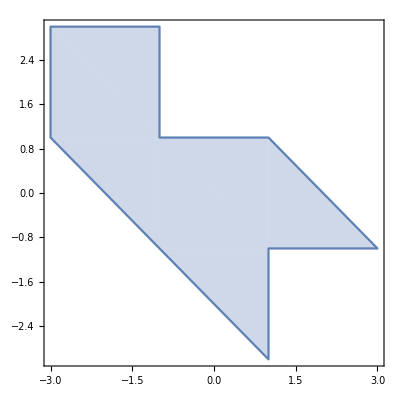

```mathematica
Subscript[T, 4]=Triangle[{{-1,1},{-3,1},{-1,-1}}];
Subscript[T, 5]=Triangle[{{-1,-1},{1,-3},{1,-1}}];
Subscript[T, 6]=Triangle[{ {1,-1},{3,-1},{1,1} }];
Subscript[R, 3]=Rectangle[{-3,1},{-1,3}];
Subscript[R, 4]=Rectangle[{-1,-1},{1,1}];
ID2=RegionUnion[Subscript[T, 4],Subscript[T, 5],Subscript[T, 6],Subscript[R, 3],Subscript[R, 4]];
RegionPlot[ID2]
```

```mathematica
(* solve Helmholtz equation on ID1 and ID2 *)
SetPrecision[NDEigenvalues[{Llin,BcondLin},u[t,x,y],t,{x,y}∈ID1,20,
Method->{"Eigensystem"->"Arnoldi","SpatialDiscretization"->{"FiniteElement","InterpolationOrder"->{u->2},"IntegrationOrder"->5,"MeshOptions"->{  "MaxCellMeasure"->0.0005, "NodeReordering"->False}}}],10]
```

{-1.585758354,1.585758354,-1.90828419,1.90828419,-2.269625962,2.269625962,-2.555770694,2.555770694,2.684054022,-2.684054022,3.031680953,-3.031680953,3.250999945,-3.250999945,-3.396601435,3.396601435,-3.512386369,3.512386369,-3.604269525,3.604269525}

```mathematica
%[[1]]-Out[74][[1]]
```

0.000677395

```mathematica
SetPrecision[NDEigenvalues[{Llin,BcondLin},u[t,x,y],t,{x,y}∈ID2,20,
Method->{"Eigensystem"->"Arnoldi","SpatialDiscretization"->{"FiniteElement","InterpolationOrder"->{u->2},"IntegrationOrder"->5,"MeshOptions"->{ "MaxCellMeasure"->0.0005, "NodeReordering"->False}}}],10]
```

{-1.592157389,1.592157389,1.909097531,-1.909097531,-2.272500656,2.272500656,-2.55603062,2.55603062,-2.690579231,2.690579231,3.034483408,-3.034483408,-3.253336514,3.253336514,3.396842349,-3.396842349,3.512406668,-3.512406668,3.612677605,-3.612677605}

```mathematica
%[[1]]-%%%[[1]]
```

-0.006399035